EconMult >

# EconMult

EconMult is a fleet model designed to be a part of a bioeconomic simulation model. First of all EconMult is meant to perform numerical calculations, but it may also be capable of doing simple analytical operations.

XXXX.

```mathematica
Needs["EconMult`EconMult`"];
```

```mathematica
SetOptions[SurplusProduction,UseMSY->False,IntrinsicGrowthRate->.5,BiomassMaximum->1000];
```

```mathematica
BioUnitAtTime[1,t_]:=(BioUnitAtTime[1,t]=BioUnitAtTime[1,t-1]+SurplusProduction[CurrentBiomass->BioUnitAtTime[1,t-1]]-Part[Flatten@EMfleetCatch[EMe:>EMtempDaysOfFishing],1])
```

```mathematica
BioUnitAtTime[1,1]=950;
```

```mathematica
EMsetup[]
```

No biomass vector was found. Assuming single value

No fleet vector was found. Assuming single value

No period interval was found. Assuming single value

EconMult structure:
1 targeted species (pEMtargetedSpecies)
1 biounit (EMrelatedBioUnits)
1 fleet group (pEMfleetUnits)
1 simulation period per year (EMinterval)

```mathematica
bEMuseCM=True;
EMelOfEffortIsOneQ=True;
```

```mathematica
pEMelOfBiomass={{{1}}};
pEMcatchability={{{.000002}}};
EMfleet={{400}};
EMdaysOfFishing={{300}};
EMunitPrice={{{9}}};
pEMfixedCost={{0}};
pEMvariableEffortCost={{.01}};
pEMvariableCatchCost={{0}};
```

```mathematica
Do[EconMult[],{41}]
```

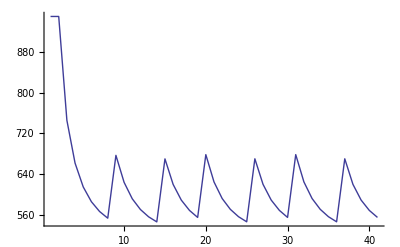

```mathematica
ListLinePlot[Flatten@hEMyearTargetBiomass,PlotRange->{0,All}]
```

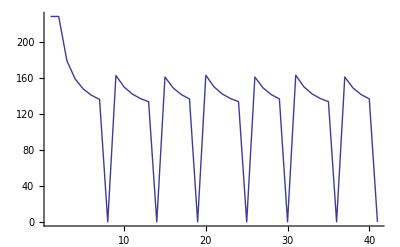

```mathematica
ListLinePlot[Flatten@hEMyearTargetCatch,PlotRange->{0,All}]
```

```mathematica
EMdaysOfFishing
```

{{300}}

```mathematica
EMtempDaysOfFishing
```

{{0}}

```mathematica
EMbiomassCatch[]
```

{162.786}

```mathematica
EMbiomassCatch[EMe->EMtempDaysOfFishing]
```

{0}

```mathematica
EMtempVesselCatch*EMfleet
```

{{{0}}}

```mathematica
EMvesselCatch[]*EMfleet
```

{{{162.786}}}

```mathematica
EMvesselCatch[EMe->EMtempDaysOfFishing]*EMfleet
```

{{{0}}}

```mathematica
EMvesselProfit[EMe->EMtempDaysOfFishing]
```

{{0}}

```mathematica
EMvesselProfit[]
```

{{0.662684}}

```mathematica
Needs["EconMult`EconMult`"];
```

```mathematica
EMsetup[{{1}},2,1]
```

EconMult structure:
1 targeted species (pEMtargetedSpecies)
1 biounit (EMrelatedBioUnits)
2 fleet groups (pEMfleetUnits)
1 simulation period per year (EMinterval)

```mathematica
EMelOfEffortIsOneQ=True;
bEMuseCM=True;
```

```mathematica
pEMelOfBiomass={{{1},{.4}}};
pEMcatchability={{{.000002},{.000029}}};
EMfleet={{500,400}};
EMdaysOfFishing={{300,200}};
EMunitPrice={{{9},{10}}};
pEMfixedCost={{0,0}};
pEMvariableEffortCost={{.015,.004}};
pEMvariableCatchCost={{0,0}};
```

```mathematica
SetOptions[SurplusProduction,UseMSY->False,IntrinsicGrowthRate->.5,BiomassMaximum->1000];
```

```mathematica
BioUnitAtTime[1,t_]:=(BioUnitAtTime[1,t]=BioUnitAtTime[1,t-1]+SurplusProduction[CurrentBiomass->BioUnitAtTime[1,t-1]]-Total@Flatten@EMfleetCatch[EMe:>EMtempDaysOfFishing])
```

```mathematica
BioUnitAtTime[1,1]=950;
```

```mathematica
effort={};
```

```mathematica
Do[EconMult[];AppendTo[effort,EMfleet*EMtempDaysOfFishing],{40}]
```

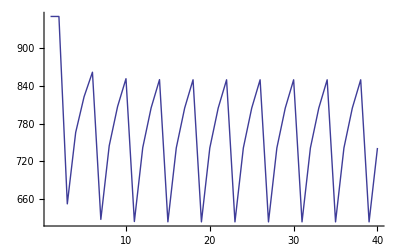

```mathematica
ListLinePlot[Flatten@hEMyearTargetBiomass,PlotRange->{0,All}]
```

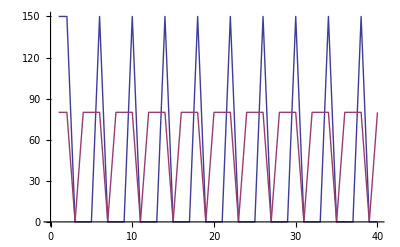

```mathematica
ListLinePlot[Transpose[Total /@ effort]/1000]
```

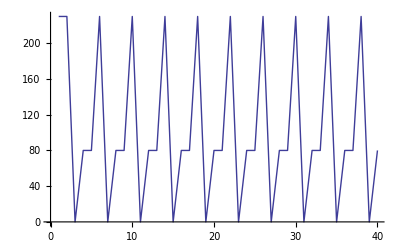

```mathematica
ListLinePlot[Total /@ Total /@ effort/1000]
```